```mathematica
tau1[A_,B_]:=24+2 √(A B)-3(A+B);
tau1[ρ A,ρ B]
Solve[tau1[ρ A,ρ B]==0,ρ]
```

24+2 √(A B ρ^2)-3 (A ρ+B ρ)

{{ρ→(24 (3 A-2 √A √B+3 B))/(9 A^2+14 A B+9 B^2)},{ρ→(24 (3 A+2 √A √B+3 B))/(9 A^2+14 A B+9 B^2)}}

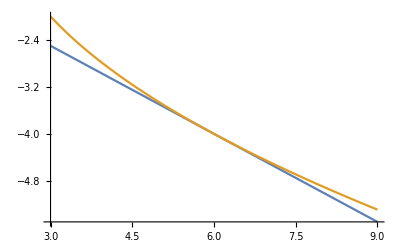

```mathematica
Plot[{-(b+2)/2,-2 √(b-2)},{b,3,9}]
```

```mathematica
isMonotone[DDX0_,DDX1_]:={
v=X1-X0;
h=(U1-U0)/2;
A0=DX0*2*h/v;
B0=DX1*2*h/v;
C0=DDX0*h*(h/v);
D0=DDX1*h*(h/v);
a=B0;
b=4*(B0-D0);
c=30-6*(D0+C0+2*B0+2*A0);
d=4*(A0+C0);
e=A0;
alpha=b*a^(-3/4)*e^(-1/4);
beta=c*a^(-1/2)*e^(-1/2);
gamma=d*a^(-1/4)*e^(-3/4);
alpha=Collect[Simplify[Expand[alpha]],{DDX0,DDX1}];
beta=Collect[Simplify[Expand[beta]],{DDX0,DDX1}];
gamma=Collect[Simplify[Expand[gamma]],{DDX0,DDX1}];
Print["α: ",alpha];
Print["β: ",beta];
Print["γ: ",gamma];
}[[1]];
isMonotone[DDX0,DDX1];
(*Print["\n-------------------------------------\n"]
Solve[alpha==(-(beta+2)/2)==gamma,{DDX0,DDX1}]*)
(*Print["\n-------------------------------------\n"]
Solve[alpha==(-2 √(beta-2))==gamma,{DDX0,DDX1}]*)
```

α: (4 ((DX1 (U0-U1))/(X0-X1))^(1/4))/((DX0 (U0-U1))/(X0-X1))^(1/4)+(DDX1 (U0-U1) ((DX1 (U0-U1))/(X0-X1))^(1/4))/(DX1 ((DX0 (U0-U1))/(X0-X1))^(1/4))

β: (3 DDX0 (U0^2-2 U0 U1+U1^2))/(2 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) (X0-X1))+(3 DDX1 (U0^2-2 U0 U1+U1^2))/(2 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) (X0-X1))+(3 (-8 DX0 U0-8 DX1 U0+8 DX0 U1+8 DX1 U1+20 X0-20 X1))/(2 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) (X0-X1))

γ: (4 DX0 ((DX1 (U0-U1))/(X0-X1))^(3/4))/(DX1 ((DX0 (U0-U1))/(X0-X1))^(3/4))+(DDX0 (-U0+U1) ((DX1 (U0-U1))/(X0-X1))^(3/4))/(DX1 ((DX0 (U0-U1))/(X0-X1))^(3/4))

```mathematica
DX0IS=DX0*(U0-U1)/(X0-X1);
DX1IS=DX1*(U0-U1)/(X0-X1);
aFunc[DDX1_]:=DDX1*((U0-U1)*DX1IS^(1/4))/(DX1*DX0IS^(1/4))+(4*DX1IS^(1/4))/DX0IS^(1/4);
gFunc[DDX0_]:=DDX0*((U1-U0)*DX1IS^(3/4))/(DX1*DX0IS^(3/4))+(4*DX0*DX1IS^(3/4))/(DX1*DX0IS^(3/4));
bFunc[DDX0_,DDX1_]:=(DDX0+DDX1)*(3*(U0-U1)^2)/(2*(X0-X1)*DX0IS^(1/2)*DX1IS^(1/2))+(24*(DX0+DX1)*(U1-U0)+60*(X0-X1))/(2*(X0-X1)*DX0IS^(1/2)*DX1IS^(1/2));
Print["α: ",aFunc[DDX1]];
Print["β: ",bFunc[DDX0,DDX1]];
Print["γ: ",gFunc[DDX0]];
Print["-----------------------------------------------------------------------------"]
Print["α: ",Collect[Simplify[Expand[aFunc[DDX1]]],{DDX0,DDX1}]];
Print["β: ",Collect[Simplify[Expand[bFunc[DDX0,DDX1]]],{DDX0,DDX1}]];
Print["γ: ",Collect[Simplify[Expand[gFunc[DDX0]]],{DDX0,DDX1}]];
```

α: (4 ((DX1 (U0-U1))/(X0-X1))^(1/4))/((DX0 (U0-U1))/(X0-X1))^(1/4)+(DDX1 (U0-U1) ((DX1 (U0-U1))/(X0-X1))^(1/4))/(DX1 ((DX0 (U0-U1))/(X0-X1))^(1/4))

β: (3 (DDX0+DDX1) (U0-U1)^2)/(2 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) (X0-X1))+(24 (DX0+DX1) (-U0+U1)+60 (X0-X1))/(2 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) (X0-X1))

γ: (4 DX0 ((DX1 (U0-U1))/(X0-X1))^(3/4))/(DX1 ((DX0 (U0-U1))/(X0-X1))^(3/4))+(DDX0 (-U0+U1) ((DX1 (U0-U1))/(X0-X1))^(3/4))/(DX1 ((DX0 (U0-U1))/(X0-X1))^(3/4))

-----------------------------------------------------------------------------

α: (4 ((DX1 (U0-U1))/(X0-X1))^(1/4))/((DX0 (U0-U1))/(X0-X1))^(1/4)+(DDX1 (U0-U1) ((DX1 (U0-U1))/(X0-X1))^(1/4))/(DX1 ((DX0 (U0-U1))/(X0-X1))^(1/4))

β: (3 DDX0 (U0^2-2 U0 U1+U1^2))/(2 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) (X0-X1))+(3 DDX1 (U0^2-2 U0 U1+U1^2))/(2 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) (X0-X1))+(3 (-8 DX0 U0-8 DX1 U0+8 DX0 U1+8 DX1 U1+20 X0-20 X1))/(2 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) (X0-X1))

γ: (4 DX0 ((DX1 (U0-U1))/(X0-X1))^(3/4))/(DX1 ((DX0 (U0-U1))/(X0-X1))^(3/4))+(DDX0 (-U0+U1) ((DX1 (U0-U1))/(X0-X1))^(3/4))/(DX1 ((DX0 (U0-U1))/(X0-X1))^(3/4))